# Analyze Märklin track signal

## Get complementary signals from digitizing car

### Load file

```mathematica
Directory[]
```

/home/cmaier/scad/Maerklin/analysis

```mathematica
Dimensions[raw=Import["TTL.10ms.5V.csv"]]
```

{524290,4}

```mathematica
Take[raw,12]
```

{{X,CH1,CH2,},{Second,Volt,Volt,},{-0.131112,5.4,0.,},{-0.131112,5.4,0.,},{-0.131111,5.4,0.,},{-0.131111,5.4,0.,},{-0.13111,5.4,0.,},{-0.13111,5.4,0.,},{-0.131109,5.4,0.,},{-0.131109,5.4,0.,},{-0.131108,5.4,0.,},{-0.131108,5.4,0.,}}

### Convert into two time series

```mathematica
Dimensions[timeseries=Transpose[{{#⟦1⟧,#⟦2⟧},{#⟦1⟧,#⟦3⟧}}&/@Drop[raw,2],{2,1,3}]]
```

{2,524288,2}

#### Calculate time step

```mathematica
Dimensions[ListConvolve[{1,-1},First/@#]&/@timeseries]
```

{2,524287}

```mathematica
GraphicsGrid[{ListPlot[ListConvolve[{1,-1},First/@#],Frame->True,PlotRange->All]}&/@timeseries]
```

-Graphics-

```mathematica
{Min[#],Max[#]}&[ListConvolve[{1,-1},First/@#]]&/@timeseries
```

{{0.,1.×10^-6},{0.,1.×10^-6}}

The time stamps have a quantization error because the precision at the beginning and end is only 1μs.

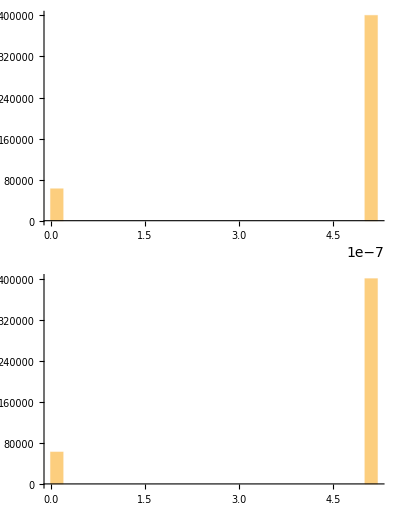

```mathematica
GraphicsGrid[{Histogram[ListConvolve[{1,-1},First/@#,PlotRange->All]]}&/@timeseries]
```

```mathematica
timestep=Mean[Median[ListConvolve[{1,-1},First/@#]]&/@timeseries]
```

5.×10^-7

### Display

```mathematica
ListPlot[Take[#,{55000,155000}]&/@timeseries,Frame->True,Joined->True]
```

-Graphics-

## Digitize time series

```mathematica
Dimensions[digitized=Map[{#⟦1⟧,HeavisideTheta[#⟦2⟧-3.0001]}&,timeseries,{2}]]
```

{2,524288,2}

### Display

```mathematica
ListPlot[Take[#,{55000,155000}]&/@digitized,Frame->True,Joined->True]
```

-Graphics-

#### Display complementary phases

```mathematica
ListPlot[MapThread[Function[{series, offset},#+{0,offset}&/@series],{digitized,{0,-1.2}}],Frame->True,Joined->True,PlotRange->All,FrameLabel->{"t [s]",""}]
```

-Graphics-

The data sent repeats every 50ms

#### Display one 50ms data transmission

```mathematica
ListPlot[Take[#,{255000,355000}]&/@MapThread[Function[{series, offset},#+{0,offset}&/@series],{digitized,{0,-1.2}}],Frame->True,Joined->True,PlotRange->All,FrameLabel->{"t [s]",""}]
```

-Graphics-

### Difference of time series

The zeros show where the phases do not overlap

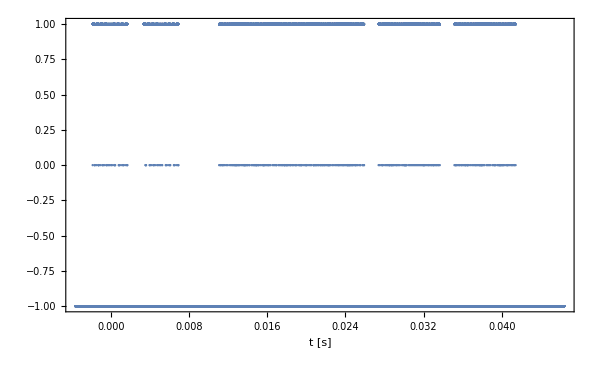

```mathematica
ListPlot[Take[MapThread[{(#1⟦1⟧+#2⟦1⟧)/2,#1⟦2⟧-#2⟦2⟧}&,digitized],{255000,355000}],Frame->True,Joined->False,PlotRange->All,FrameLabel->{"t [s]",""}]
```

#### Runs of identical values for difference series

```mathematica
Dimensions/@(diffruns=SplitBy[Take[MapThread[{(#1⟦1⟧+#2⟦1⟧)/2,#1⟦2⟧-#2⟦2⟧}&,digitized],{255000,355000}],Last])
```

{{3497,2},{1,2},{363,2},{1,2},{51,2},{51,2},{2,2},{362,2},{1,2},{361,2},{2,2},{51,2},{1,2},{51,2},{1,2},{361,2},{1,2},{362,2},{1,2},{51,2},{51,2},{2,2},{362,2},{1,2},{361,2},{1,2},{51,2},{1,2},{51,2},{1,2},{361,2},{1,2},{51,2},{1,2},{362,2},{51,2},{2,2},{361,2},{1,2},{361,2},{2,2},{50,2},{1,2},{52,2},{1,2},{362,2},{362,2},{1,2},{51,2},{1,2},{50,2},{2,2},{361,2},{1,2},{362,2},{1,2},{52,2},{52,2},{2,2},{362,2},{1,2},{361,2},{1,2},{51,2},{1,2},{51,2},{1,2},{3347,2},{362,2},{1,2},{51,2},{1,2},{50,2},{2,2},{362,2},{363,2},{1,2},{51,2},{51,2},{2,2},{362,2},{1,2},{361,2},{1,2},{51,2},{1,2},{51,2},{1,2},{361,2},{1,2},{362,2},{1,2},{51,2},{51,2},{1,2},{362,2},{1,2},{52,2},{1,2},{361,2},{1,2},{51,2},{1,2},{362,2},{362,2},{1,2},{51,2},{1,2},{51,2},{1,2},{362,2},{1,2},{361,2},{2,2},{51,2},{52,2},{1,2},{362,2},{362,2},{1,2},{52,2},{1,2},{51,2},{1,2},{361,2},{1,2},{362,2},{1,2},{50,2},{1,2},{51,2},{1,2},{8329,2},{1,2},{199,2},{1,2},{100,2},{1,2},{199,2},{1,2},{199,2},{1,2},{99,2},{2,2},{199,2},{100,2},{1,2},{97,2},{197,2},{1,2},{197,2},{1,2},{197,2},{1,2},{197,2},{198,2},{1,2},{197,2},{1,2},{196,2},{1,2},{198,2},{1,2},{99,2},{1,2},{100,2},{100,2},{1,2},{99,2},{1,2},{99,2},{1,2},{99,2},{1,2},{98,2},{2,2},{97,2},{1,2},{198,2},{1,2},{100,2},{1,2},{96,2},{1,2},{199,2},{1,2},{99,2},{1,2},{98,2},{197,2},{1,2},{196,2},{1,2},{199,2},{1,2},{100,2},{1,2},{98,2},{2,2},{99,2},{1,2},{100,2},{1,2},{99,2},{1,2},{97,2},{1,2},{198,2},{1,2},{99,2},{1,2},{98,2},{197,2},{2,2},{196,2},{199,2},{1,2},{100,2},{98,2},{1,2},{197,2},{1,2},{196,2},{2,2},{199,2},{1,2},{99,2},{1,2},{99,2},{1,2},{99,2},{2,2},{97,2},{1,2},{199,2},{1,2},{99,2},{1,2},{97,2},{1,2},{200,2},{100,2},{1,2},{97,2},{198,2},{1,2},{198,2},{1,2},{98,2},{2,2},{99,2},{1,2},{100,2},{1,2},{97,2},{1,2},{196,2},{1,2},{197,2},{1,2},{199,2},{1,2},{99,2},{1,2},{98,2},{1,2},{197,2},{1,2},{196,2},{1,2},{198,2},{198,2},{1,2},{197,2},{1,2},{197,2},{1,2},{197,2},{1,2},{197,2},{2,2},{197,2},{198,2},{1,2},{197,2},{1,2},{196,2},{1,2},{196,2},{1,2},{196,2},{2,2},{199,2},{99,2},{1,2},{100,2},{1,2},{99,2},{2,2},{97,2},{1,2},{198,2},{1,2},{100,2},{1,2},{96,2},{2,2},{196,2},{1,2},{199,2},{1,2},{99,2},{100,2},{1,2},{100,2},{1,2},{97,2},{1,2},{200,2},{100,2},{1,2},{100,2},{1,2},{199,2},{1,2},{99,2},{199,2},{2,2},{199,2},{1,2},{99,2},{1,2},{200,2},{200,2},{1,2},{99,2},{1,2},{199,2},{2,2},{199,2},{1,2},{99,2},{2,2},{201,2},{200,2},{1,2},{99,2},{199,2},{2,2},{198,2},{1,2},{99,2},{2,2},{198,2},{100,2},{1,2},{98,2},{198,2},{1,2},{197,2},{1,2},{197,2},{1,2},{198,2},{199,2},{2,2},{99,2},{1,2},{98,2},{1,2},{199,2},{1,2},{99,2},{1,2},{97,2},{1,2},{197,2},{1,2},{198,2},{1,2},{100,2},{1,2},{98,2},{196,2},{2,2},{196,2},{1,2},{196,2},{2,2},{196,2},{1,2},{196,2},{2,2},{196,2},{1,2},{197,2},{1,2},{197,2},{1,2},{199,2},{2,2},{99,2},{1,2},{100,2},{1,2},{99,2},{1,2},{100,2},{1,2},{100,2},{98,2},{1,2},{198,2},{197,2},{2,2},{197,2},{197,2},{1,2},{197,2},{1,2},{197,2},{1,2},{196,2},{1,2},{196,2},{2,2},{196,2},{1,2},{197,2},{1,2},{196,2},{1,2},{199,2},{1,2},{99,2},{1,2},{97,2},{1,2},{197,2},{1,2},{197,2},{1,2},{196,2},{1,2},{198,2},{2,2},{99,2},{1,2},{100,2},{1,2},{99,2},{1,2},{97,2},{2,2},{198,2},{1,2},{99,2},{1,2},{97,2},{1,2},{197,2},{2,2},{196,2},{1,2},{199,2},{1,2},{198,2},{1,2},{98,2},{2,2},{198,2},{1,2},{199,2},{1,2},{100,2},{199,2},{1,2},{199,2},{1,2},{100,2},{1,2},{199,2},{199,2},{1,2},{98,2},{1,2},{195,2},{2,2},{2991,2},{1,2},{199,2},{1,2},{100,2},{200,2},{1,2},{199,2},{1,2},{99,2},{2,2},{199,2},{100,2},{1,2},{98,2},{198,2},{1,2},{197,2},{1,2},{196,2},{1,2},{197,2},{1,2},{199,2},{2,2},{99,2},{1,2},{98,2},{1,2},{199,2},{1,2},{99,2},{2,2},{97,2},{1,2},{197,2},{2,2},{199,2},{100,2},{1,2},{97,2},{197,2},{2,2},{196,2},{1,2},{196,2},{1,2},{197,2},{1,2},{196,2},{1,2},{197,2},{197,2},{1,2},{197,2},{1,2},{198,2},{1,2},{100,2},{1,2},{99,2},{2,2},{99,2},{1,2},{98,2},{2,2},{99,2},{1,2},{98,2},{1,2},{197,2},{197,2},{1,2},{196,2},{1,2},{197,2},{1,2},{197,2},{1,2},{197,2},{1,2},{197,2},{1,2},{196,2},{1,2},{196,2},{1,2},{197,2},{1,2},{196,2},{1,2},{199,2},{1,2},{100,2},{98,2},{1,2},{196,2},{1,2},{196,2},{1,2},{197,2},{1,2},{198,2},{2,2},{98,2},{1,2},{100,2},{1,2},{98,2},{1,2},{97,2},{1,2},{199,2},{100,2},{1,2},{98,2},{197,2},{2,2},{196,2},{1,2},{199,2},{1,2},{199,2},{1,2},{100,2},{1,2},{199,2},{1,2},{199,2},{2,2},{99,2},{1,2},{199,2},{1,2},{198,2},{1,2},{100,2},{1,2},{199,2},{1,2},{198,2},{1,2},{100,2},{1,2},{195,2},{1,2},{2990,2},{1,2},{199,2},{2,2},{98,2},{1,2},{198,2},{2,2},{199,2},{100,2},{1,2},{199,2},{1,2},{100,2},{1,2},{98,2},{197,2},{2,2},{196,2},{1,2},{197,2},{1,2},{197,2},{1,2},{199,2},{2,2},{99,2},{1,2},{98,2},{1,2},{199,2},{1,2},{99,2},{2,2},{97,2},{1,2},{197,2},{1,2},{200,2},{100,2},{1,2},{98,2},{197,2},{1,2},{197,2},{1,2},{197,2},{1,2},{196,2},{1,2},{196,2},{2,2},{196,2},{1,2},{197,2},{1,2},{196,2},{1,2},{199,2},{2,2},{99,2},{1,2},{100,2},{1,2},{99,2},{1,2},{99,2},{2,2},{98,2},{1,2},{97,2},{1,2},{196,2},{1,2},{197,2},{1,2},{198,2},{197,2},{1,2},{197,2},{1,2},{197,2},{1,2},{196,2},{1,2},{196,2},{1,2},{197,2},{197,2},{1,2},{196,2},{1,2},{199,2},{1,2},{99,2},{1,2},{97,2},{2,2},{197,2},{197,2},{1,2},{197,2},{1,2},{198,2},{2,2},{99,2},{1,2},{100,2},{1,2},{99,2},{1,2},{97,2},{2,2},{198,2},{1,2},{99,2},{1,2},{97,2},{1,2},{197,2},{2,2},{197,2},{199,2},{1,2},{198,2},{1,2},{98,2},{2,2},{198,2},{1,2},{199,2},{1,2},{100,2},{199,2},{1,2},{198,2},{1,2},{100,2},{1,2},{199,2},{1,2},{199,2},{1,2},{100,2},{1,2},{196,2},{1,2},{9960,2}}

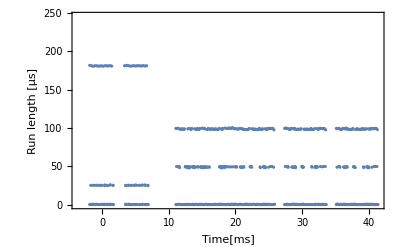

```mathematica
ListPlot[{10^3 First[First[#]],10^6 timestep Length[#]}&/@diffruns,Frame->True,FrameLabel->{"Time[ms]","Run length [μs]"}]
```

In the difference series, the short run lengths of the phase non-overlaps are visible.

#### Runs of identical values for each series

```mathematica
Map[Dimensions,runs=SplitBy[Take[#,{255000,355000}],Last]&/@digitized,{2}]
```

{{{3497,2},{365,2},{51,2},{53,2},{362,2},{364,2},{51,2},{53,2},{361,2},{364,2},{51,2},{53,2},{362,2},{363,2},{51,2},{53,2},{361,2},{53,2},{362,2},{53,2},{361,2},{364,2},{50,2},{54,2},{362,2},{363,2},{51,2},{53,2},{361,2},{364,2},{52,2},{54,2},{362,2},{363,2},{51,2},{53,2},{3347,2},{363,2},{51,2},{53,2},{362,2},{364,2},{51,2},{53,2},{362,2},{363,2},{51,2},{53,2},{361,2},{364,2},{51,2},{52,2},{362,2},{54,2},{361,2},{53,2},{362,2},{363,2},{51,2},{53,2},{362,2},{364,2},{51,2},{53,2},{362,2},{363,2},{52,2},{53,2},{361,2},{364,2},{50,2},{53,2},{8329,2},{201,2},{100,2},{201,2},{199,2},{102,2},{199,2},{101,2},{97,2},{198,2},{197,2},{199,2},{197,2},{199,2},{197,2},{198,2},{198,2},{101,2},{100,2},{101,2},{99,2},{101,2},{99,2},{101,2},{97,2},{200,2},{100,2},{98,2},{199,2},{101,2},{98,2},{198,2},{196,2},{201,2},{100,2},{101,2},{99,2},{102,2},{99,2},{99,2},{198,2},{101,2},{98,2},{199,2},{196,2},{200,2},{100,2},{99,2},{197,2},{199,2},{199,2},{101,2},{99,2},{102,2},{97,2},{201,2},{99,2},{99,2},{200,2},{101,2},{97,2},{199,2},{198,2},{101,2},{99,2},{102,2},{97,2},{198,2},{197,2},{201,2},{99,2},{100,2},{197,2},{198,2},{198,2},{199,2},{197,2},{199,2},{197,2},{200,2},{197,2},{199,2},{197,2},{198,2},{196,2},{199,2},{199,2},{100,2},{100,2},{102,2},{97,2},{200,2},{100,2},{99,2},{196,2},{201,2},{99,2},{101,2},{100,2},{99,2},{200,2},{101,2},{100,2},{201,2},{99,2},{201,2},{199,2},{101,2},{200,2},{201,2},{99,2},{202,2},{199,2},{102,2},{201,2},{201,2},{99,2},{201,2},{198,2},{102,2},{198,2},{101,2},{98,2},{199,2},{197,2},{199,2},{198,2},{201,2},{99,2},{100,2},{199,2},{101,2},{97,2},{199,2},{198,2},{102,2},{98,2},{198,2},{196,2},{199,2},{196,2},{199,2},{196,2},{199,2},{197,2},{202,2},{99,2},{102,2},{99,2},{102,2},{100,2},{99,2},{198,2},{199,2},{197,2},{198,2},{197,2},{199,2},{196,2},{199,2},{196,2},{199,2},{196,2},{201,2},{99,2},{99,2},{197,2},{199,2},{196,2},{201,2},{99,2},{102,2},{99,2},{100,2},{198,2},{101,2},{97,2},{200,2},{196,2},{201,2},{198,2},{101,2},{198,2},{201,2},{100,2},{200,2},{199,2},{102,2},{199,2},{200,2},{98,2},{198,2},{2991,2},{201,2},{100,2},{201,2},{199,2},{102,2},{199,2},{101,2},{98,2},{199,2},{197,2},{198,2},{197,2},{202,2},{99,2},{100,2},{199,2},{102,2},{97,2},{200,2},{199,2},{101,2},{97,2},{199,2},{196,2},{198,2},{197,2},{198,2},{197,2},{198,2},{197,2},{200,2},{100,2},{102,2},{99,2},{101,2},{99,2},{100,2},{197,2},{198,2},{196,2},{199,2},{197,2},{199,2},{197,2},{198,2},{196,2},{199,2},{196,2},{201,2},{100,2},{99,2},{196,2},{198,2},{197,2},{201,2},{98,2},{102,2},{98,2},{99,2},{199,2},{101,2},{98,2},{199,2},{196,2},{201,2},{199,2},{102,2},{199,2},{202,2},{99,2},{201,2},{198,2},{102,2},{199,2},{200,2},{100,2},{197,2},{2990,2},{202,2},{98,2},{201,2},{199,2},{101,2},{199,2},{102,2},{98,2},{199,2},{196,2},{199,2},{197,2},{202,2},{99,2},{100,2},{199,2},{102,2},{97,2},{199,2},{200,2},{101,2},{98,2},{198,2},{197,2},{199,2},{196,2},{199,2},{196,2},{199,2},{196,2},{202,2},{99,2},{102,2},{99,2},{102,2},{98,2},{99,2},{196,2},{199,2},{198,2},{198,2},{197,2},{199,2},{196,2},{198,2},{197,2},{198,2},{196,2},{201,2},{99,2},{100,2},{197,2},{198,2},{197,2},{201,2},{99,2},{102,2},{99,2},{100,2},{198,2},{101,2},{97,2},{200,2},{197,2},{200,2},{198,2},{101,2},{198,2},{201,2},{100,2},{200,2},{198,2},{102,2},{199,2},{201,2},{100,2},{198,2},{9960,2}},{{3498,2},{363,2},{52,2},{51,2},{365,2},{361,2},{54,2},{51,2},{363,2},{362,2},{52,2},{51,2},{365,2},{361,2},{53,2},{51,2},{363,2},{51,2},{363,2},{51,2},{364,2},{361,2},{53,2},{52,2},{363,2},{362,2},{53,2},{50,2},{364,2},{362,2},{53,2},{52,2},{365,2},{361,2},{53,2},{51,2},{3348,2},{362,2},{53,2},{50,2},{364,2},{363,2},{52,2},{51,2},{365,2},{361,2},{53,2},{51,2},{363,2},{362,2},{52,2},{51,2},{364,2},{52,2},{363,2},{51,2},{363,2},{362,2},{53,2},{51,2},{364,2},{361,2},{53,2},{52,2},{363,2},{362,2},{54,2},{51,2},{363,2},{362,2},{52,2},{51,2},{8331,2},{199,2},{102,2},{199,2},{201,2},{99,2},{201,2},{100,2},{98,2},{197,2},{199,2},{197,2},{198,2},{198,2},{199,2},{196,2},{200,2},{99,2},{101,2},{100,2},{101,2},{99,2},{101,2},{98,2},{100,2},{198,2},{102,2},{96,2},{201,2},{99,2},{99,2},{197,2},{198,2},{199,2},{102,2},{98,2},{102,2},{100,2},{101,2},{97,2},{200,2},{99,2},{99,2},{197,2},{198,2},{199,2},{101,2},{98,2},{199,2},{196,2},{202,2},{99,2},{101,2},{99,2},{100,2},{199,2},{101,2},{97,2},{201,2},{100,2},{98,2},{198,2},{200,2},{98,2},{102,2},{100,2},{99,2},{196,2},{199,2},{199,2},{101,2},{98,2},{199,2},{196,2},{199,2},{198,2},{199,2},{197,2},{199,2},{197,2},{199,2},{198,2},{199,2},{196,2},{198,2},{196,2},{201,2},{99,2},{102,2},{99,2},{100,2},{198,2},{102,2},{96,2},{199,2},{199,2},{100,2},{100,2},{102,2},{97,2},{201,2},{100,2},{102,2},{199,2},{100,2},{199,2},{202,2},{99,2},{201,2},{200,2},{101,2},{199,2},{202,2},{99,2},{203,2},{200,2},{100,2},{199,2},{201,2},{99,2},{200,2},{100,2},{99,2},{198,2},{199,2},{197,2},{199,2},{199,2},{102,2},{98,2},{201,2},{99,2},{99,2},{197,2},{200,2},{100,2},{99,2},{196,2},{199,2},{196,2},{199,2},{196,2},{199,2},{197,2},{199,2},{199,2},{102,2},{100,2},{101,2},{100,2},{101,2},{98,2},{199,2},{197,2},{199,2},{197,2},{199,2},{197,2},{198,2},{196,2},{199,2},{197,2},{198,2},{199,2},{101,2},{97,2},{199,2},{197,2},{198,2},{198,2},{102,2},{100,2},{101,2},{97,2},{201,2},{99,2},{99,2},{197,2},{199,2},{199,2},{200,2},{98,2},{201,2},{199,2},{101,2},{199,2},{201,2},{100,2},{200,2},{199,2},{100,2},{195,2},{2994,2},{199,2},{101,2},{200,2},{201,2},{99,2},{201,2},{100,2},{99,2},{198,2},{199,2},{196,2},{199,2},{199,2},{102,2},{98,2},{201,2},{99,2},{100,2},{197,2},{201,2},{100,2},{98,2},{197,2},{199,2},{196,2},{199,2},{196,2},{198,2},{197,2},{199,2},{198,2},{102,2},{99,2},{102,2},{98,2},{102,2},{98,2},{198,2},{197,2},{198,2},{197,2},{199,2},{197,2},{199,2},{196,2},{198,2},{197,2},{198,2},{199,2},{101,2},{98,2},{198,2},{196,2},{199,2},{198,2},{101,2},{100,2},{100,2},{97,2},{200,2},{100,2},{99,2},{197,2},{199,2},{199,2},{201,2},{100,2},{201,2},{199,2},{102,2},{199,2},{200,2},{100,2},{201,2},{198,2},{102,2},{195,2},{2992,2},{199,2},{101,2},{198,2},{201,2},{100,2},{201,2},{100,2},{99,2},{197,2},{199,2},{197,2},{199,2},{199,2},{102,2},{98,2},{201,2},{99,2},{100,2},{197,2},{201,2},{100,2},{99,2},{197,2},{199,2},{197,2},{198,2},{196,2},{199,2},{197,2},{198,2},{199,2},{102,2},{100,2},{101,2},{99,2},{101,2},{97,2},{198,2},{197,2},{199,2},{197,2},{199,2},{197,2},{198,2},{196,2},{198,2},{197,2},{198,2},{199,2},{101,2},{97,2},{199,2},{197,2},{199,2},{198,2},{102,2},{100,2},{101,2},{97,2},{201,2},{99,2},{99,2},{197,2},{199,2},{199,2},{200,2},{98,2},{201,2},{199,2},{101,2},{199,2},{200,2},{100,2},{201,2},{199,2},{102,2},{196,2},{9961,2}}}

```mathematica
Length/@runs
```

{421,421}

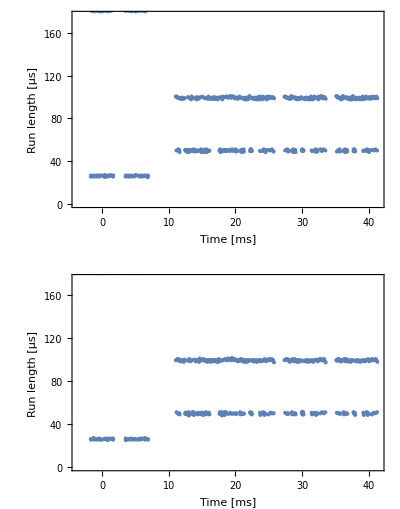

```mathematica
GraphicsGrid[{ListPlot[{10^3 First[First[#]],10^6 timestep Length[#]}&/@#,Frame->True,FrameLabel->{"Time [ms]","Run length [μs]"}]}&/@runs]
```

It is clearly apparent that the short modulation bursts have a different encoding timing than the remaining long and medium length bursts.

## Packets within the time series

### Short data packets

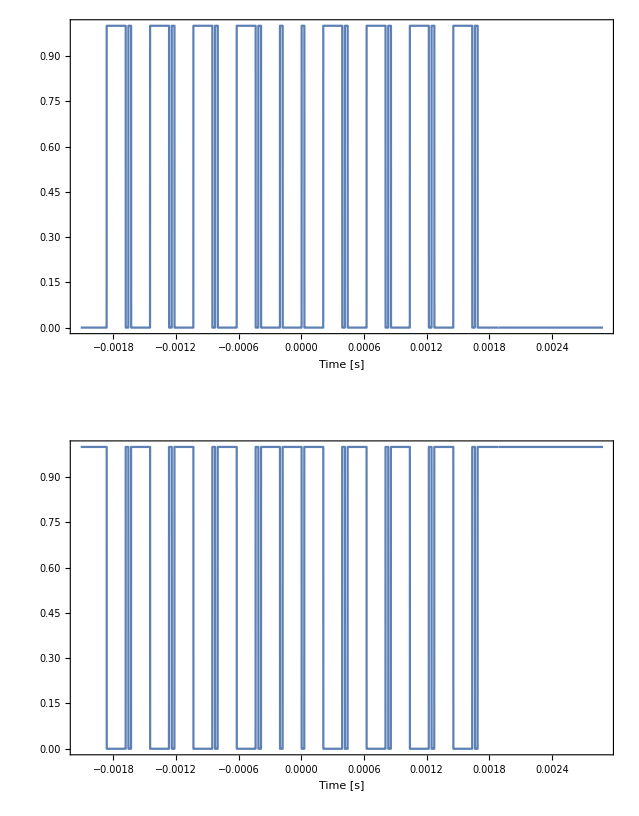

```mathematica
GraphicsGrid[{ListPlot[Take[#,{258000,268000}],Frame->True,Joined->True,FrameLabel->{"Time [s]",""}]}&/@digitized]
```

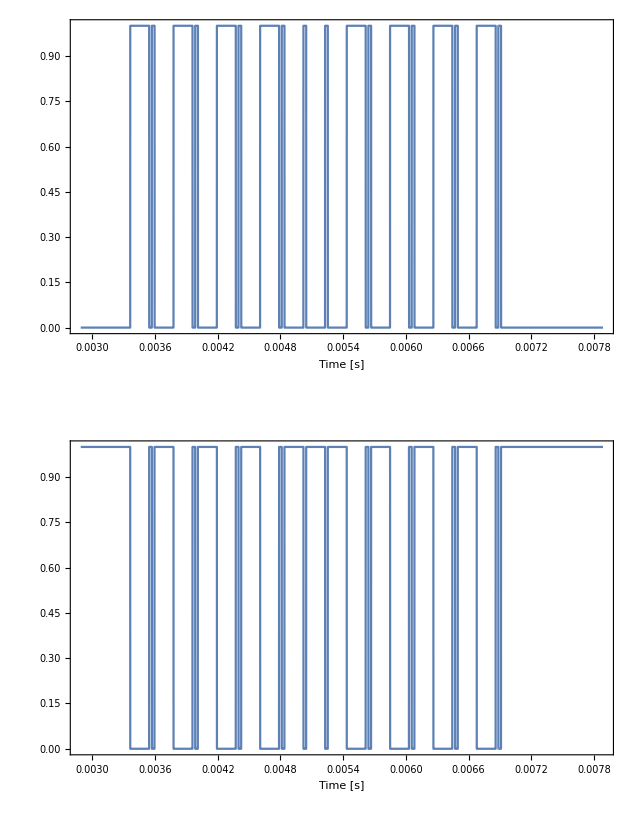

```mathematica
GraphicsGrid[{ListPlot[Take[#,{268000,278000}],Frame->True,Joined->True,FrameLabel->{"Time [s]",""}]}&/@digitized]
```